## Imports and helper functions

```mathematica
Needs["QM`"];
Needs["QuantumWalks`"];
Needs["GeneralUtilities`"];
Needs["MaTeX`"];

Get[FileNameJoin@{NotebookDirectory[],"stabilityAnalysis.m"}];
Get[FileNameJoin@{NotebookDirectory[],"searchCoinParameters.m"}];
```

```mathematica
normalizePhase[expr_?MatrixQ]:=expr Exp[-I Arg@expr⟦1,1⟧]//Chop;
normalizePhase[expr_List]:=expr Exp[-I Arg@expr⟦1⟧]//Chop;
```

```mathematica
MF[args___]:=MatrixForm[args];
exportHere[name_,obj_]:=Export[FileNameJoin@{NotebookDirectory[],name},obj];
texStyles=<|"plain"->Directive[Black,{FontFamily->"LM Roman 12",FontSize->24,FontWeight->Plain,FontSlant->Plain}],"writing"->Directive[Black,{FontFamily->"CMU Serif",FontSize->20,FontWeight->Plain,FontSlant->Plain}],"title"->Directive[Black,{FontFamily->"CMU Serif",FontSize->24,FontWeight->Plain,FontSlant->Plain}],"labels"->Directive[Black,{FontFamily->"LMMathItalic10",FontSize->24,FontWeight->Plain,FontSlant->Plain}]|>;
ClearAll@monitorMap;
Attributes@monitorMap=HoldAll;
monitorMap[Map[func_,target_]]:=Module[{iter=0},
Monitor[
Map[(iter++;func@#)&,target],
progressBar[100.iter/Length@target]
]
];
```

## Some examples of numerical optimization

The numerical optimization technique described in the paper is here implemented in searchCoinParameters.
This function, given a number of steps and a target state, computes the fidelity between the output state obtained with a given set of values for the coin parameters, and the target state. This expression of the fidelity depending on the set of coin parameters is fed into a global maximization function like NMaximize, which then finds the values corresponding to an optimal (namely, unitary) fidelity.

Two different methods are here used:
	1) Naive optimization. The expression for the fidelity is computed symbolically using standard high-level Mathematica functions. This becomes impractical very quickly for larger number of steps, but does not require precompilation time. To use this method pass the option "CacheFinalExpression"→False to 	searchCoinParameters.
	2) Compiled optimization. Uses the same numerical maximization as above, but the expression for the fidelity is compiled down to C code, making the procedure much faster, at the cost of additional time required for the compilation before the maximization begins. Moreover, caching is enabled: once the expression for the fidelity for a given number of steps and a given target state has been compiled down to C, the compiled expression is stored to be used later (which reduces the overall compilation time).

IMPORTANT: when using caching (enabled by default), always clear the cache before running the optimization again with a different target state (for example with ClearAll@searchCoinParameters`Cache).

```mathematica
searchCoinParameters[2,Normalize@{1,1,1},"IncludeProjectionInMaximization"->False]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.161865,ξ[1]→3.47679×10^-13,θ[2]→-0.0565467,ξ[2]→-1.93634×10^-13},TargetState→{1/(√3),1/(√3),1/(√3)}|>

```mathematica
searchCoinParameters[2,Normalize@{1,1,1},"IncludeProjectionInMaximization"->True]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→1.11602,ξ[1]→1.68277×10^-8,θ[2]→-0.571147,ξ[2]→-1.37267×10^-8,α→-0.454775},TargetState→{1/(√3),1/(√3),1/(√3)}|>

```mathematica
searchCoinParameters[3,"CacheFinalExpression"->False]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→1.54223,ξ[1]→1.05649,θ[2]→0.0532829,ξ[2]→-1.84811,θ[3]→0.0693212,ξ[3]→-0.687983,α→-0.064567},TargetState→{0.252508-0.0300588 ⅈ,-0.289673+0.374407 ⅈ,0.588718-0.183028 ⅈ,-0.314508+0.481914 ⅈ}|>

```mathematica
searchCoinParameters@4
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.665141,ξ[1]→0.758771,θ[2]→1.19561,ξ[2]→0.871049,θ[3]→0.461983,ξ[3]→-1.24772,θ[4]→0.988946,ξ[4]→1.67073,α→0.835092},TargetState→{0.0357867+0.285353 ⅈ,0.0695693-0.535017 ⅈ,0.311729+0.286173 ⅈ,-0.256265+0.565131 ⅈ,-0.0807586-0.23574 ⅈ}|>

```mathematica
searchCoinParameters[16]
```

Preparing state...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.548399,ξ[1]→-1.60549,θ[2]→-0.32799,ξ[2]→0.82442,θ[3]→-0.559397,ξ[3]→-0.249807,θ[4]→0.170735,ξ[4]→-1.78282,θ[5]→-0.212279,ξ[5]→-0.26565,θ[6]→0.520152,ξ[6]→0.770685,θ[7]→-0.0898036,ξ[7]→-1.80286,θ[8]→-0.598958,ξ[8]→1.01529,θ[9]→-0.367818,ξ[9]→-0.943748,θ[10]→-0.544037,ξ[10]→-0.346591,θ[11]→0.28355,ξ[11]→1.249,θ[12]→0.196596,ξ[12]→-2.21237,θ[13]→0.0884568,ξ[13]→1.04096,θ[14]→0.40156,ξ[14]→1.44294,θ[15]→0.304103,ξ[15]→0.490536,θ[16]→-0.732568,ξ[16]→-1.13172,α→0.287311},TargetState→{-0.0774168+0.101679 ⅈ,-0.19186-0.309913 ⅈ,-0.305452-0.241714 ⅈ,-0.282115+0.258144 ⅈ,0.187544+0.0887374 ⅈ,-0.0634965+0.241294 ⅈ,0.0257516+0.0255446 ⅈ,-0.0438302+0.0522665 ⅈ,-0.0320538-0.144271 ⅈ,0.145288-0.0295 ⅈ,-0.0824504-0.120532 ⅈ,0.000745154+0.231325 ⅈ,0.308358+0.180276 ⅈ,0.0838724-0.108508 ⅈ,-0.318567+0.0354144 ⅈ,0.0480467+0.0612026 ⅈ,-0.260001+0.0119203 ⅈ}|>

```mathematica
searchCoinParameters[18]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-0.113646,ξ[1]→-1.12684,θ[2]→0.232767,ξ[2]→1.97495,θ[3]→0.136369,ξ[3]→-2.4821,θ[4]→-0.427588,ξ[4]→3.51222,θ[5]→0.502012,ξ[5]→-2.23244,θ[6]→0.160807,ξ[6]→0.247411,θ[7]→-0.475824,ξ[7]→2.82248,θ[8]→-0.0874949,ξ[8]→-1.16653,θ[9]→-0.439227,ξ[9]→-2.07452,θ[10]→0.964141,ξ[10]→3.19859,θ[11]→0.312325,ξ[11]→-1.01453,θ[12]→-0.500146,ξ[12]→-1.73032,θ[13]→0.273343,ξ[13]→1.43924,θ[14]→0.883295,ξ[14]→-2.55915,θ[15]→0.0511211,ξ[15]→2.39495,θ[16]→0.53244,ξ[16]→-4.2225,θ[17]→-0.492912,ξ[17]→6.2876,θ[18]→0.163891,ξ[18]→-4.52845,α→0.319297},TargetState→{-0.142108-0.186354 ⅈ,-0.0828464+0.167931 ⅈ,-0.072903+0.0925074 ⅈ,0.0915877+0.131127 ⅈ,0.176411-0.310163 ⅈ,-0.175018+0.368767 ⅈ,-0.202673-0.0870255 ⅈ,-0.212676+0.10307 ⅈ,-0.0616935-0.0700044 ⅈ,0.107343-0.0383104 ⅈ,-0.0995424+0.159586 ⅈ,0.0974586-0.0668138 ⅈ,-0.157557+0.0937719 ⅈ,0.0663314+0.444099 ⅈ,-0.188984-0.122751 ⅈ,0.0953867-0.214851 ⅈ,-0.17628-0.116672 ⅈ,-0.0684874+0.0641229 ⅈ,-0.0706436+0.0362134 ⅈ}|>

```mathematica
searchCoinParameters[19]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.389123,ξ[1]→2.62485,θ[2]→-0.142109,ξ[2]→-0.320269,θ[3]→-0.0771792,ξ[3]→-2.31096,θ[4]→-0.0901666,ξ[4]→0.401009,θ[5]→-0.146583,ξ[5]→0.865706,θ[6]→-0.227461,ξ[6]→-1.78075,θ[7]→-0.220477,ξ[7]→1.41383,θ[8]→-0.131009,ξ[8]→-1.7188,θ[9]→-0.390627,ξ[9]→-1.06634,θ[10]→0.805042,ξ[10]→3.58746,θ[11]→-0.0917951,ξ[11]→-2.02425,θ[12]→-0.239607,ξ[12]→-0.70142,θ[13]→0.0587003,ξ[13]→3.22778,θ[14]→-0.120406,ξ[14]→-4.98421,θ[15]→-0.0446196,ξ[15]→4.43531,θ[16]→0.247714,ξ[16]→-1.56283,θ[17]→0.326776,ξ[17]→0.942496,θ[18]→-0.418913,ξ[18]→-1.21273,θ[19]→-0.249062,ξ[19]→0.694083,α→-0.0921486},TargetState→{0.0845797+0.00184606 ⅈ,0.215023+0.10752 ⅈ,-0.228767-0.150652 ⅈ,-0.46937+0.194271 ⅈ,-0.139088+0.0880715 ⅈ,0.109255-0.103948 ⅈ,-0.0714009-0.199896 ⅈ,-0.0133229+0.0792844 ⅈ,0.0449405-0.0638268 ⅈ,-0.0616721-0.00634475 ⅈ,0.244809+0.435102 ⅈ,0.00238555-0.0758821 ⅈ,0.0208189-0.0306149 ⅈ,0.0273469+0.123265 ⅈ,-0.00161174-0.0970476 ⅈ,-0.0351658-0.0681872 ⅈ,0.120742-0.1546 ⅈ,-0.0507374+0.0921184 ⅈ,-0.0949382+0.0630903 ⅈ,0.00460154+0.374811 ⅈ}|>

```mathematica
searchCoinParameters[19]//AbsoluteTiming
```

Preparing state...

Starting maximization...

{17.0132,<|FinalFidelity→1.,CoinParameters→{θ[1]→0.634022,ξ[1]→3.45214,θ[2]→-0.411611,ξ[2]→-0.853793,θ[3]→-0.353461,ξ[3]→0.606971,θ[4]→0.653535,ξ[4]→-2.10997,θ[5]→0.208935,ξ[5]→0.710142,θ[6]→-0.382362,ξ[6]→1.08828,θ[7]→-0.160182,ξ[7]→0.347788,θ[8]→0.333308,ξ[8]→-1.44505,θ[9]→-0.283309,ξ[9]→1.57745,θ[10]→-0.0603926,ξ[10]→-2.61955,θ[11]→-0.623552,ξ[11]→-1.82707,θ[12]→0.0208418,ξ[12]→0.460501,θ[13]→0.323543,ξ[13]→2.17608,θ[14]→0.414068,ξ[14]→-0.991863,θ[15]→0.220162,ξ[15]→-0.685197,θ[16]→0.259022,ξ[16]→-0.0707604,θ[17]→0.471407,ξ[17]→3.13375,θ[18]→0.61416,ξ[18]→-2.52703,θ[19]→-0.147351,ξ[19]→1.6021,α→-0.512725},TargetState→{0.078793+0.171506 ⅈ,-0.0499455+0.128547 ⅈ,-0.114772+0.315436 ⅈ,0.155422+0.143577 ⅈ,-0.0421968-0.206983 ⅈ,-0.0342044+0.216584 ⅈ,-0.0394148-0.321175 ⅈ,0.0489696+0.0302937 ⅈ,-0.161575+0.0933658 ⅈ,0.263669-0.355781 ⅈ,0.0790485-0.231129 ⅈ,-0.0296718-0.196954 ⅈ,0.118875-0.0996238 ⅈ,0.191948+0.0725141 ⅈ,-0.138463+0.0547618 ⅈ,0.0891946+0.013418 ⅈ,0.195953+0.0413679 ⅈ,0.189155-0.0569184 ⅈ,-0.161577+0.0349822 ⅈ,0.0386334-0.22915 ⅈ}|>}

```mathematica
searchCoinParameters[19]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→0.879312,ξ[1]→-0.486134,θ[2]→-0.200577,ξ[2]→0.676995,θ[3]→-0.161979,ξ[3]→0.484546,θ[4]→-0.563197,ξ[4]→-0.0104582,θ[5]→0.265956,ξ[5]→0.0944432,θ[6]→0.26815,ξ[6]→0.253688,θ[7]→0.202788,ξ[7]→-0.652344,θ[8]→-0.694164,ξ[8]→-0.47791,θ[9]→-0.27709,ξ[9]→0.239733,θ[10]→0.0205322,ξ[10]→-0.760334,θ[11]→0.0735008,ξ[11]→-1.84398,θ[12]→-0.246785,ξ[12]→3.38556,θ[13]→0.533642,ξ[13]→-2.26742,θ[14]→-0.558401,ξ[14]→2.24527,θ[15]→-0.153483,ξ[15]→-0.814475,θ[16]→0.575795,ξ[16]→0.44226,θ[17]→0.771946,ξ[17]→0.693813,θ[18]→-0.462713,ξ[18]→0.343423,θ[19]→0.299738,ξ[19]→-0.611963,α→0.633356},TargetState→{-0.0499348-0.176962 ⅈ,0.00282451+0.0697927 ⅈ,0.0154358-0.0905819 ⅈ,-0.113515-0.396088 ⅈ,0.246969-0.103046 ⅈ,0.0497041-0.273779 ⅈ,0.0969721+0.0979089 ⅈ,0.144582+0.254866 ⅈ,-0.125203+0.0278645 ⅈ,0.0548062+0.22841 ⅈ,0.110981+0.0828225 ⅈ,-0.0559435-0.181087 ⅈ,-0.135893+0.25429 ⅈ,0.0693368-0.016569 ⅈ,0.132904+0.244274 ⅈ,-0.213125+0.130693 ⅈ,-0.0375462-0.223907 ⅈ,0.0393973-0.100805 ⅈ,-0.0616367-0.183654 ⅈ,-0.13272+0.236718 ⅈ}|>

```mathematica
searchCoinParameters[22]
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-1.53308,ξ[1]→1.07755,θ[2]→0.274433,ξ[2]→-3.61175,θ[3]→-0.365929,ξ[3]→3.32387,θ[4]→-0.388033,ξ[4]→-0.213769,θ[5]→0.35957,ξ[5]→-0.395987,θ[6]→-0.400849,ξ[6]→0.190918,θ[7]→-0.345945,ξ[7]→-4.58646,θ[8]→-0.224549,ξ[8]→4.67026,θ[9]→0.714968,ξ[9]→-2.95312,θ[10]→-0.335599,ξ[10]→2.3408,θ[11]→0.574149,ξ[11]→-1.08057,θ[12]→-0.154701,ξ[12]→-1.4559,θ[13]→-0.164958,ξ[13]→1.82178,θ[14]→-0.31993,ξ[14]→-0.0407475,θ[15]→-0.49833,ξ[15]→-2.71022,θ[16]→0.579721,ξ[16]→2.76145,θ[17]→-0.228785,ξ[17]→0.656945,θ[18]→-0.258606,ξ[18]→-2.03814,θ[19]→0.646426,ξ[19]→0.625873,θ[20]→-0.241043,ξ[20]→0.24058,θ[21]→0.30575,ξ[21]→-1.57021,θ[22]→-0.217445,ξ[22]→-0.154587,α→-1.08543},TargetState→{-0.0194276+0.00580265 ⅈ,-0.12086-0.0582444 ⅈ,-0.0136564+0.0123361 ⅈ,0.101534-0.00672679 ⅈ,-0.0275473-0.155773 ⅈ,-0.193491-0.0050662 ⅈ,0.202528+0.0467882 ⅈ,-0.20569-0.282096 ⅈ,0.209385-0.103155 ⅈ,-0.191502+0.154342 ⅈ,0.149488+0.061889 ⅈ,0.160862-0.163186 ⅈ,-0.035835+0.0366376 ⅈ,0.0343749+0.239339 ⅈ,0.152045-0.0377801 ⅈ,0.0284754+0.0951359 ⅈ,-0.184034-0.32421 ⅈ,0.128818+0.193029 ⅈ,-0.087186+0.0905856 ⅈ,-0.24776-0.0876825 ⅈ,0.156216-0.142554 ⅈ,0.180466+0.23559 ⅈ,-0.200588-0.0583879 ⅈ}|>

## Analysis of results from maximization

The functions searchResult* can be used to recover data from the output of searchCoinParameters.

```mathematica
Get[FileNameJoin@{NotebookDirectory[],"searchCoinParameters.m"}];
```

```mathematica
ClearAll@searchCoinParameters`Cache;
out=searchCoinParameters@4
```

Preparing state...

Compiling function for caching...

Starting maximization...

<|FinalFidelity→1.,CoinParameters→{θ[1]→-1.2538,ξ[1]→-0.481991,θ[2]→0.66552,ξ[2]→2.29153,θ[3]→0.300674,ξ[3]→-0.412986,θ[4]→-0.881843,ξ[4]→-0.516986,α→0.975057},TargetState→{-0.0841002-0.101962 ⅈ,-0.200858-0.0553485 ⅈ,-0.636388+0.293188 ⅈ,0.263433-0.159895 ⅈ,-0.124346+0.581162 ⅈ}|>

```mathematica
searchResultGetCoinParameters@out
searchResultGetProjection@out
searchResultComputeFullOutput@out
searchResultComputeProjectedOutput@out
searchResultProjectionProbability@out

searchResultTestFidelity@out
```

{{-1.2538,-0.481991},{0.66552,2.29153},{0.300674,-0.412986},{-0.881843,-0.516986}}

{0.561121,0.827734}

{0.0949113+0.114709 ⅈ,0.+0. ⅈ,0.18012-0.200634 ⅈ,0.0313407+0.178039 ⅈ,0.14271-0.0557942 ⅈ,0.38887-0.18681 ⅈ,0.166917+0.525159 ⅈ,-0.314127-0.233597 ⅈ,0.+0. ⅈ,0.0942694-0.443932 ⅈ}

{0.0842572+0.101832 ⅈ,0.200944+0.055039 ⅈ,0.635936-0.294168 ⅈ,-0.263186+0.160301 ⅈ,0.123451-0.581352 ⅈ}

0.399517

1.

IMPORTANT: most (all?) of the data generated and saved in statesAndFidelities_*steps_*states*.mx has been generated using a different parametrization of the coin operators than the one now used by default. The setting $QWSU2Notation = "Old" must be used in these cases.

#### 5 steps

```mathematica
data5stepsNMax=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*5steps*_corrected.mx"};
data5stepsNMax//Length;

(*data5stepsNMaxProbs=computeProbabilityFromResult/@data5stepsNMax//monitorMap;
exportHere["nmaximize_5steps_probabilities.mx",data5stepsNMaxProbs]*)
data5stepsNMaxProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_5steps_probabilities.mx"}];
```

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data5stepsNMax,Flatten@Position[data5stepsNMax⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data5stepsNMaxProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[0,14,.5],ControlType->Slider,Appearance->"Labeled"}
]
```

Stability of solutions:

The following code is used to study the variation of the output fidelity when changing the various coin parameters. Functions from the stabilityAnalysis package are used for the purpose. This is how the plots put in the paper were produced.

```mathematica
searchCoinParameters[5,Normalize@ConstantArray[1,6],
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]
```

Preparing state...

Starting maximization...

<|FinalFidelity→0.89129181919230449083,CoinParameters→{θ[1]→-0.20564683001429986212,ξ[1]→1.0661923441725643961,θ[2]→0.42664957617269139862,ξ[2]→2.077951626225338023,θ[3]→-0.0032185555254551303343,ξ[3]→0.53082493043289675889,θ[4]→-1.0927365660276712697,ξ[4]→0.0025059571971322021091,θ[5]→-2.3015907450699344534,ξ[5]→-0.0028309012375717766149},TargetState→{1/(√6),1/(√6),1/(√6),1/(√6),1/(√6),1/(√6)}|>

```mathematica
ClearAll@searchCoinParameters`Cache;
searchCoinParameters[5,Normalize@ConstantArray[1,6],
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//stabilityAnalysis`plotFidelityVsParameters[{0.9,1.1},"TypeOfPerturbation"->Times,"ParametersToPlot"->{1,2}]
```

Preparing state...

Compiling function for caching...

Starting maximization...

-Graphics-

```mathematica
ClearAll@searchCoinParameters`Cache;
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//plotFidelityVsParameters[{0.9,1.1},"TypeOfPerturbation"->Times]
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
ClearAll@searchCoinParameters`Cache;
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False,
WorkingPrecision->20
]//plotFidelityVsParameters[{-1,1.},"TypeOfPerturbation"->Plus]
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
ClearAll@searchCoinParameters`Cache;
searchCoinParameters[5,sampleTarget,
"IncludeProjectionInMaximization"->False
]//plotFidelityVsParameters@{0.9,1.1}
```

Preparing state...

Starting maximization...

-Graphics-

```mathematica
ClearAll@searchCoinParameters`Cache;
searchCoinParameters[5,
"IncludeProjectionInMaximization"->False
]//plotFidelityVsParameters@{0.9,1.1}
```

Preparing state...

Starting maximization...

-Graphics-

#### 19 steps

```mathematica
data19steps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*19steps*_corrected.mx"};
data19steps//Length;
```

```mathematica
(*data19stepsProbs=computeProbabilityFromResult/@data19steps//monitorMap;
exportHere["nmaximize_19steps_probabilities.mx",data19stepsProbs]*)
data19stepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_19steps_probabilities.mx"}];
```

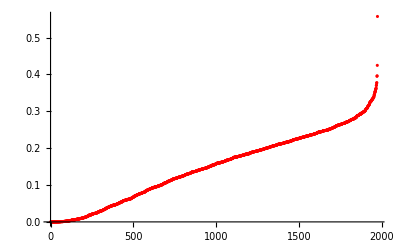

```mathematica
ListPlot[
Sort@data19stepsProbs,
PlotRange->All,PlotStyle->Red
]
```

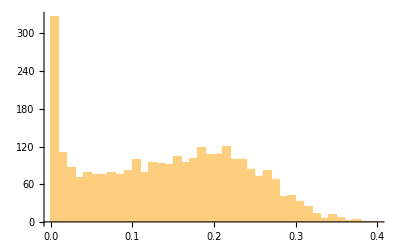

```mathematica
Histogram[data19stepsProbs,40]
```

On the other hand, let’s see what happens if we only consider the projection probabilities associated with the states obtained with good fidelities:

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data19steps,Flatten@Position[data19steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data19stepsProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[0,14,.5],ControlType->Slider,Appearance->"Labeled"}
]
```

#### 20 steps

```mathematica
data20steps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*20steps*_corrected.mx"};
```

```mathematica
computeTargetFromResult@First@data20steps
```

{-0.023324-0.313501 ⅈ,-0.00167684+0.0163723 ⅈ,0.0526861+0.187663 ⅈ,-0.0052893-0.0517087 ⅈ,-0.0696381-0.0699305 ⅈ,-0.151423+0.0710714 ⅈ,-0.243091+0.0928453 ⅈ,-0.124506+0.12365 ⅈ,0.0111806+0.0335208 ⅈ,-0.0492254-0.00381385 ⅈ,-0.128238+0.168903 ⅈ,0.160168-0.00750893 ⅈ,0.123975-0.166524 ⅈ,0.243231-0.0533927 ⅈ,-0.239693+0.139898 ⅈ,0.323715-0.0759767 ⅈ,-0.12786-0.272475 ⅈ,-0.0612236-0.149938 ⅈ,0.251398-0.0657417 ⅈ,-0.241732-0.184852 ⅈ,0.282608-0.00986604 ⅈ}

```mathematica
data20steps⟦1⟧["TargetState"]
```

{0.231453-0.212735 ⅈ,-0.0138826+0.00883889 ⅈ,-0.114531+0.157721 ⅈ,0.037281-0.03622 ⅈ,0.0116641-0.0979986 ⅈ,-0.149666-0.0747001 ⅈ,-0.2236-0.133102 ⅈ,-0.174216-0.0209757 ⅈ,-0.0193603+0.0295608 ⅈ,-0.0275389-0.040979 ⅈ,-0.212028+0.00416403 ⅈ,0.10523+0.120983 ⅈ,0.207518-0.00603266 ⅈ,0.19274+0.157682 ⅈ,-0.258402-0.101254 ⅈ,0.260373+0.206809 ⅈ,0.134435-0.269292 ⅈ,0.0796431-0.14102 ⅈ,0.207491+0.156429 ⅈ,-0.00492599-0.30427 ⅈ,0.183019+0.215568 ⅈ}

See all the obtained fidelities

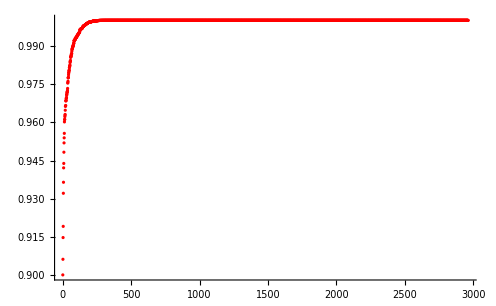

```mathematica
data20stepsSorted=SortBy[#["FinalFidelity"]&]@data20steps;
ListPlot[
data20stepsSorted⟦All,"FinalFidelity"⟧,
PlotRange->All,PlotStyle->Red
]
```

How do the projection probabilities behave?

```mathematica
data20stepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_20steps_probabilities.mx"}];
(*data20stepsProbs=computeProbabilityFromResult/@data20steps//monitorMap;*)
```

```mathematica
exportHere["nmaximize_20steps_probabilities.mx",data20stepsProbs]
```

C:\Users\lk\Documents\docs\coding\mathematica\QuantumInformation\QuantumWalks\nmaximize_20steps_probabilities.mx

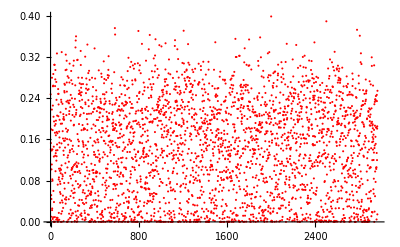

```mathematica
ListPlot[
data20stepsProbs,
PlotRange->All,PlotStyle->Red
]
```

Including all of the data we get something with an annoying peak around zero probability

```mathematica
Histogram[data20stepsProbs,40]
```

-Graphics-

On the other hand, let’s see what happens if we only consider the projection probabilities associated with the states obtained with good fidelities:

```mathematica
Manipulate[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data20steps,Flatten@Position[data20steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Histogram[
data20stepsProbs⟦onlyGoodFidelityIndices⟧,
PlotLabel->"Number of states : "<>ToString@Length@onlyGoodFidelityIndices
]
],
{{threshold,10},Range[4,14,1],ControlType->Slider,Appearance->"Labeled"}
]
```

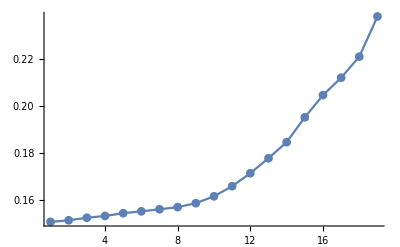

```mathematica
With[{data=Table[
With[{onlyGoodFidelityIndices=Complement[Range@Length@data20steps,Flatten@Position[data20steps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]]},
Mean@data20stepsProbs⟦onlyGoodFidelityIndices⟧
],
{threshold,4,13,.5}
]},
ListPlot[data,
PlotRange->All,Joined->True,PlotMarkers->Automatic
]
]
```

#### Visualization of projection probabilities of solutions obtained with NMaximize

```mathematica
ClearAll@probabilityHistograms2Thresholds;
Options@probabilityHistograms2Thresholds=Options@Histogram;
probabilityHistograms2Thresholds[nSteps_Integer,thresholds_List:{0,10},nBins_Integer:20,opts:OptionsPattern[]]:=Block[
{dataNSteps,dataNStepsProbs,goodIndices},
dataNSteps=Import@First@FileNames@FileNameJoin@{NotebookDirectory[],"data","*"<>ToString@nSteps<>"steps*_corrected.mx"};
dataNStepsProbs=Import[FileNameJoin@{NotebookDirectory[],"data","nmaximize_"<>ToString@nSteps<>"steps_probabilities.mx"}];

goodIndices[threshold_]:=Complement[Range@Length@dataNSteps,Flatten@Position[dataNSteps⟦All,"FinalFidelity"⟧,_?(#<1-10^-threshold&)]];

With[{data=Table[
dataNStepsProbs⟦goodIndices@threshold⟧,
{threshold,thresholds}
]},
Histogram[
data,nBins,"Count",
AxesStyle->texStyles["title"],
Evaluate@FilterRules[{opts},Options@Histogram]
]
]
];
```

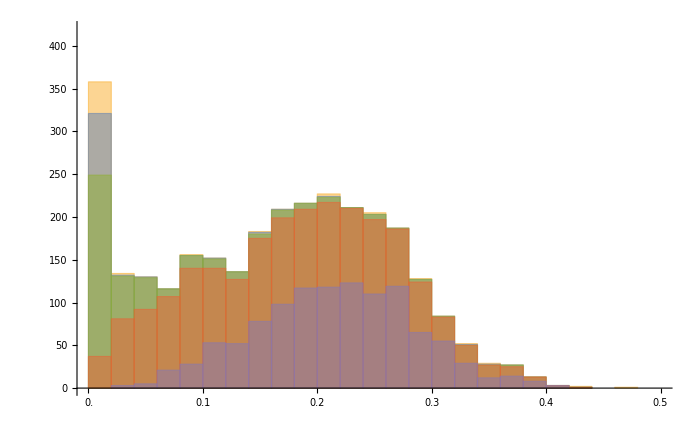

C:\Users\lk\Documents\docs\research\Quantum Walks (2016-2017)\code\probsHistogram_15steps_manyThresholds.pdf

```mathematica
fig2save=probabilityHistograms2Thresholds[15,{0,2,5,10,12},
PlotRange->{{0,.5},{0,420}},Ticks->{Range[0,.5,.05],Automatic},
ImageSize->700
]
exportHere["probsHistogram_15steps_manyThresholds.pdf",fig2save]
```

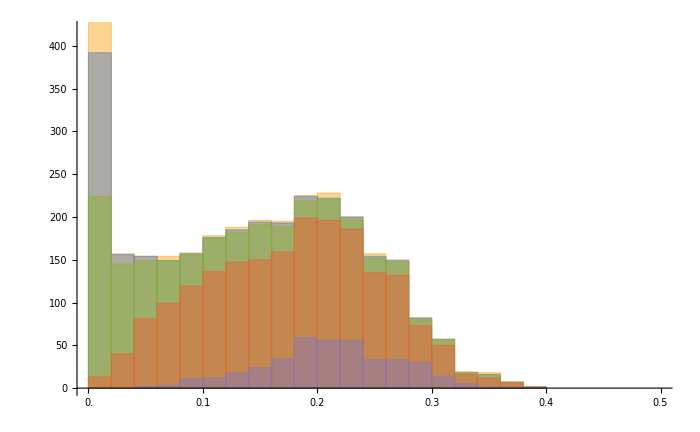

C:\Users\lk\Documents\docs\research\Quantum Walks (2016-2017)\code\probsHistogram_20steps_manyThresholds.pdf

```mathematica
fig2save=probabilityHistograms2Thresholds[20,{0,2,5,10,12},
PlotRange->{{0,.5},{0,420}},Ticks->{Range[0,.5,.05],Automatic},
ImageSize->700
]
exportHere["probsHistogram_20steps_manyThresholds.pdf",fig2save]
```

```mathematica
Manipulate[
probabilityHistograms2Thresholds[
nSteps,{0,firstThreshold,5,10,12},
PlotRange->{{0,.5},{0,450}},ImageSize->500
],
{{nSteps,20},4,20,1,Appearance->"Labeled"},
{{firstThreshold,2},0,14,1,Appearance->"Labeled"}
]
```